{{aTrue→(-aMeas+aBad f)/(-1+f)}}

deltaA =

Abs[((-aBad+aMeas) f)/(-1+f)]/aMeas

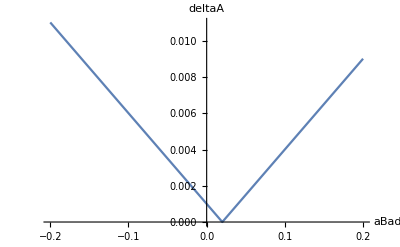

0.00900901

```mathematica
(* solve for deltaA := |aMeas-aTrue|/aMeas, with f the fraction of events in aBad *)
ClearAll[aMeas,f,aBad,aTrue,deltaA,deltaAfn,aTrueSol]
aTrueSol=Solve[
aMeas==f*aBad+(1-f)*aTrue,
aTrue
]
Print["deltaA ="]
deltaA=FullSimplify[
Abs[
aMeas-(aTrue/.aTrueSol[[1]])
]/aMeas
];
deltaAfn[aBad_]=deltaA
(* plug in numbers and plot deltaA vs. aBad *)
aMeas=0.02;
f=0.001;
Plot[
deltaAfn[a],
{a,-10*aMeas,10*aMeas},
PlotRange->Automatic,
AxesLabel->{"aBad","deltaA"}
]
(* evaluate deltaA for a specific value of aBad *)
deltaAfn[10*aMeas]
```